```mathematica
list={{{0,0},0},{{0,-1},0},{{0,-2},0},{{0,-3},0},{{-1,-3},0},{{-1,-4},0},{{-1,-5},0},{{-2,-5},0},{{-3,-5},0},{{-4,-5},0}}
```

{{{0,0},0},{{0,-1},0},{{0,-2},0},{{0,-3},0},{{-1,-3},0},{{-1,-4},0},{{-1,-5},0},{{-2,-5},0},{{-3,-5},0},{{-4,-5},0}}

```mathematica
Length[list]
```

10

```mathematica
list={{0,0},{0,-1},{0,-2},{0,-3},{-1,-3},{-1,-4},{-1,-5},{-2,-5},{-3,-5},{-4,-5}}
```

{{0,0},{0,-1},{0,-2},{0,-3},{-1,-3},{-1,-4},{-1,-5},{-2,-5},{-3,-5},{-4,-5}}

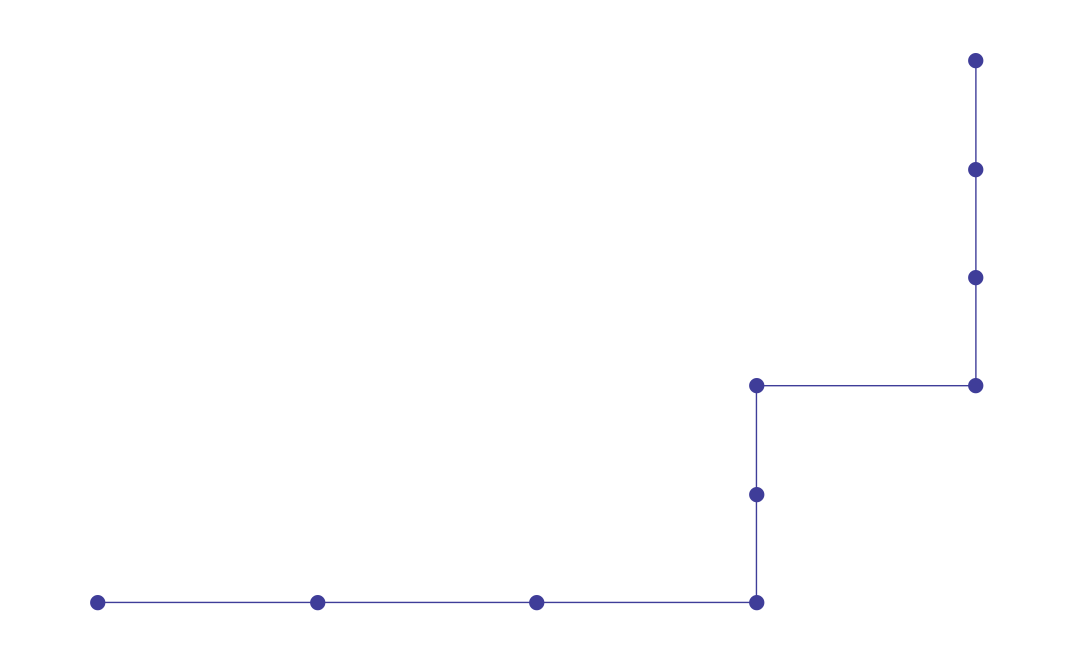

```mathematica
ListPlot[list,Joined->True,PlotMarkers->{Automatic,20},Axes->False]
```

```mathematica
test1={{0,0},{0,-2},{0,-3}}
```

{{0,0},{0,-2},{0,-3}}

```mathematica
Union[test1,test2]
```

{{-1,-3},{0,-3},{0,-2},{0,-1},{0,0}}

```mathematica
test2={{0,-1},{-1,-3}}
```

{{0,-1},{-1,-3}}

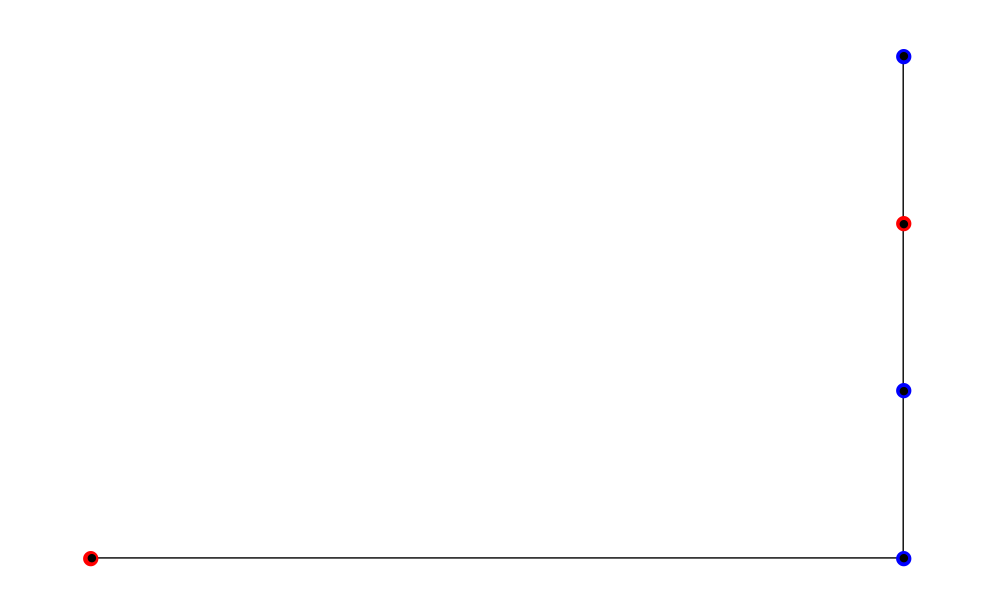

```mathematica
ListPlot[{test1,test2,{{0,0},{0,-1},{0,-2},{0,-3},{-1,-3}}},Joined->{False,False,True},PlotMarkers->{{●,20},{●,20},{●,0}},PlotStyle->{Blue,Red,Black},Axes->False]
```

```mathematica
list2={{0,0},{0,-1},{1,-1},{1,0},{2,0},{2,-1},{3,-1},{3,0},{4,0},{4,-1}}
```

{{0,0},{0,-1},{1,-1},{1,0},{2,0},{2,-1},{3,-1},{3,0},{4,0},{4,-1}}

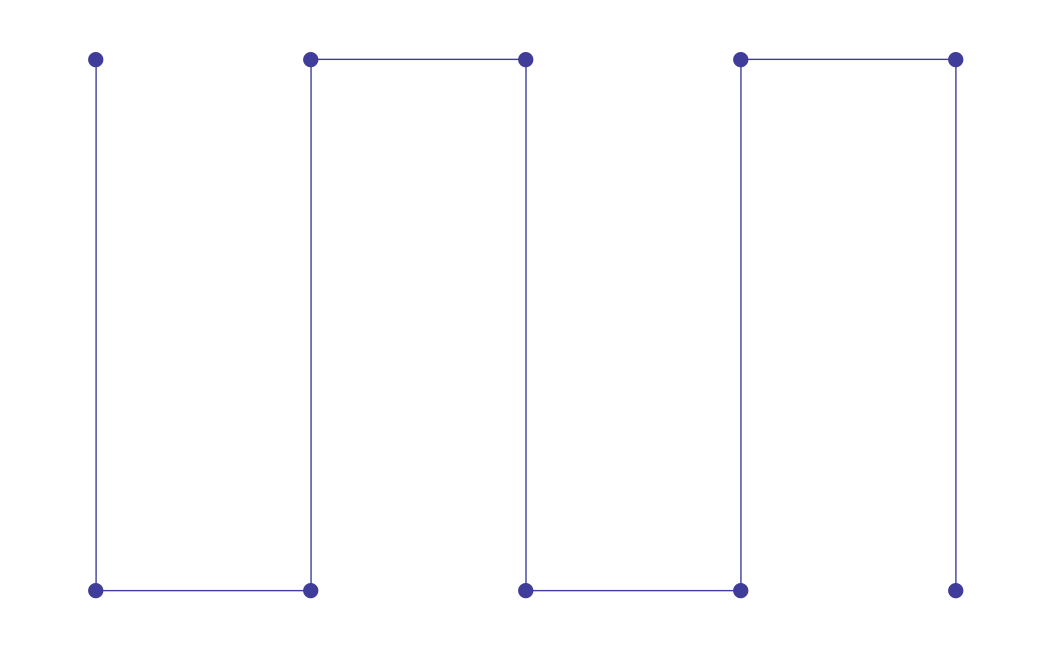

```mathematica
ListPlot[list2,Joined->True,PlotMarkers->{Automatic,20},Axes->False]
```

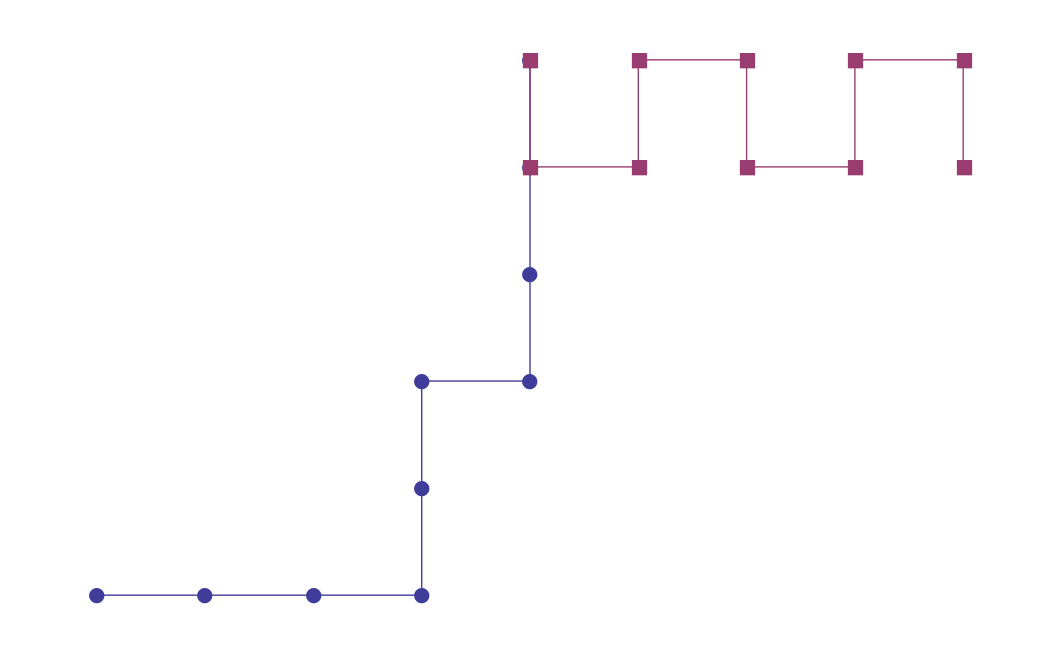

```mathematica
ListPlot[{list,list2},Joined->True,PlotMarkers->{Automatic,20},Axes->False]
```

```mathematica
PutAppend[{5,6},"testing.txt"]
```

```mathematica
(*calcualte Rg!!!*)
```

```mathematica
Do[
readln=ReadList[StringJoin["!cat /home/singaram/data/rosenbluth/linear/chain_100/0.5/microstates_0.5_99.txt | ","awk -v var=",ToString[i]," 'NR==var'"]];
polymerconfig=First[readln];
 PolyCoors={};
Do[
(*Print[polymerconfig[[j]][[1]]];*)
 PolyCoors=Append[PolyCoors,polymerconfig[[j]][[1]]];
,{j,1,Length[polymerconfig]}];

 CoorPairs=Subsets[PolyCoors,{2}];
Rg=0;
Do[
(*you are computing Rg^2, so be sure to square root after teh average*)
Rg=Rg+((0.01)^2)*SquaredEuclideanDistance[CoorPairs[[k]][[1]],CoorPairs[[k]][[2]]];
,{k,1,Length[CoorPairs]}];
PutAppend[Sqrt[Rg],"/home/singaram/data/rosenbluth/linear/chain_100/0.5/Rg.txt"];
,{i,1,466432}];
```

$Aborted

```mathematica
10^-5.93 = x^2/(10*10^-3-x)
```

```mathematica
Solve[10^-5.93 == x^2/(10*10^-3-x),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.000108982},{x→0.000107807}}

```mathematica
testconfig={{{1,1},1},{{1,2},0},{{2,3},1}}
```

{{{1,1},1},{{1,2},0},{{2,3},1}}

```mathematica
polycoors={};
```

```mathematica
Do[
 polycoors=Append[polycoors,testconfig[[i]][[1]]];
,{i,1,Length[testconfig]}];
```

```mathematica
polycoors
```

{{1,1},{1,2},{2,3}}

```mathematica
coorpairs=Subsets[polycoors,{2}]
```

{{{1,1},{1,2}},{{1,1},{2,3}},{{1,2},{2,3}}}

```mathematica
Rg=0
```

0

```mathematica
Do[
Rg=Rg+SquaredEuclideanDistance[coorpairs[[i]][[1]],coorpairs[[i]][[2]]];


,{i,1,Length[coorpairs]}];
```

```mathematica
N[Sqrt[Rg]/3]
```

0.942809

```mathematica
(*polymer config half covered and 50 sites*)
```

```mathematica
polyconfig={{{0,0},0},{{0,-1},0},{{1,-1},1},{{1,-2},1},{{0,-2},1},{{-1,-2},0},{{-2,-2},0},{{-3,-2},0},{{-4,-2},0},{{-4,-1},1},{{-3,-1},1},{{-2,-1},0},{{-2,0},0},{{-3,0},1},{{-4,0},1},{{-5,0},1},{{-5,-1},1},{{-6,-1},0},{{-6,0},1},{{-7,0},1},{{-7,-1},1},{{-8,-1},1},{{-8,0},1},{{-8,1},1},{{-7,1},1},{{-6,1},1},{{-5,1},1},{{-4,1},1},{{-3,1},1},{{-3,2},1},{{-4,2},1},{{-5,2},1},{{-6,2},1},{{-7,2},1},{{-7,3},0},{{-7,4},0},{{-6,4},0},{{-6,5},0},{{-5,5},0},{{-4,5},0},{{-3,5},0},{{-3,6},0},{{-2,6},0},{{-2,7},0},{{-2,8},0},{{-2,9},0},{{-2,10},0},{{-1,10},0},{{-1,11},0},{{-2,11},0}};
```

```mathematica
Length[polyconfig]
```

50

```mathematica
Needs["MonteCarloRosenbluth`","/home/singaram/scripts/mathematica/packages/MC_Rosenbluth.m"];
```

```mathematica
(*now get occupied and unoccupied positions from polymerconfig*)
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig]
```

{{3,4,5,10,11,14,15,16,17,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34},{1,2,6,7,8,9,12,13,18,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{3,4,5,10,11,14,15,16,17,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34}

```mathematica
UnOccPosns=OccUnOccList[[2]]
```

{1,2,6,7,8,9,12,13,18,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
OccSites={}
```

{}

```mathematica
Do[
Coor=polyconfig[[posn,1]];
OccSites=Append[OccSites,Coor];
,{posn,OccPosns}];
```

```mathematica
OccSites05=OccSites
```

{{1,-1},{1,-2},{0,-2},{-4,-1},{-3,-1},{-3,0},{-4,0},{-5,0},{-5,-1},{-6,0},{-7,0},{-7,-1},{-8,-1},{-8,0},{-8,1},{-7,1},{-6,1},{-5,1},{-4,1},{-3,1},{-3,2},{-4,2},{-5,2},{-6,2},{-7,2}}

```mathematica
UnOccSites={};
```

```mathematica
Do[
Coor=polyconfig[[posn,1]];
UnOccSites=Append[UnOccSites,Coor];
,{posn,UnOccPosns}];
```

```mathematica
UnOccSites05=UnOccSites
```

{{0,0},{0,-1},{-1,-2},{-2,-2},{-3,-2},{-4,-2},{-2,-1},{-2,0},{-6,-1},{-7,3},{-7,4},{-6,4},{-6,5},{-5,5},{-4,5},{-3,5},{-3,6},{-2,6},{-2,7},{-2,8},{-2,9},{-2,10},{-1,10},{-1,11},{-2,11}}

```mathematica
polycoor={};
```

```mathematica
Do[
polycoor=Append[polycoor,polyconfig[[i,1]]];
,{i,1,50}]
```

```mathematica
polycoor05=polycoor
```

{{0,0},{0,-1},{1,-1},{1,-2},{0,-2},{-1,-2},{-2,-2},{-3,-2},{-4,-2},{-4,-1},{-3,-1},{-2,-1},{-2,0},{-3,0},{-4,0},{-5,0},{-5,-1},{-6,-1},{-6,0},{-7,0},{-7,-1},{-8,-1},{-8,0},{-8,1},{-7,1},{-6,1},{-5,1},{-4,1},{-3,1},{-3,2},{-4,2},{-5,2},{-6,2},{-7,2},{-7,3},{-7,4},{-6,4},{-6,5},{-5,5},{-4,5},{-3,5},{-3,6},{-2,6},{-2,7},{-2,8},{-2,9},{-2,10},{-1,10},{-1,11},{-2,11}}

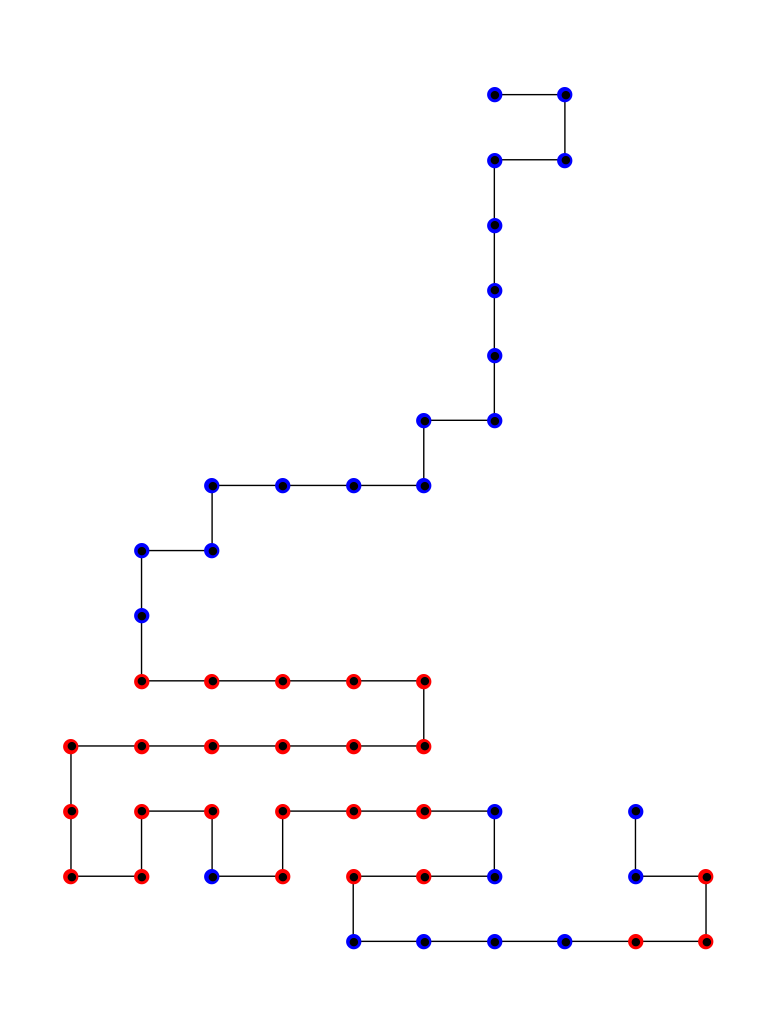

```mathematica
ListPlot[{UnOccSites05,OccSites05,polycoor05},Joined->{False,False,True},PlotMarkers->{{●,20},{●,20},{●,0}},PlotStyle->{Blue,Red,Black},Axes->False,AspectRatio->1/0.75]
```

```mathematica
(*chain length of 50 with no bound proteins*)
polyconfig={{{0,0},0},{{0,-1},0},{{1,-1},0},{{1,0},0},{{1,1},0},{{1,2},0},{{2,2},0},{{3,2},0},{{4,2},0},{{4,3},0},{{3,3},0},{{2,3},0},{{2,4},0},{{2,5},0},{{1,5},0},{{1,4},0},{{1,3},0},{{0,3},0},{{-1,3},0},{{-1,2},0},{{-2,2},0},{{-3,2},0},{{-3,1},0},{{-2,1},0},{{-2,0},0},{{-3,0},0},{{-3,-1},0},{{-3,-2},0},{{-3,-3},0},{{-4,-3},0},{{-4,-2},0},{{-4,-1},0},{{-4,0},0},{{-4,1},0},{{-4,2},0},{{-4,3},0},{{-5,3},0},{{-5,4},0},{{-5,5},0},{{-6,5},0},{{-6,6},0},{{-6,7},0},{{-5,7},0},{{-4,7},0},{{-4,8},0},{{-5,8},0},{{-6,8},0},{{-6,9},0},{{-7,9},0},{{-7,8},0}};
```

```mathematica
Length[polyconfig]
```

50

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig]
```

{{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}}

```mathematica
UnOccPosns=OccUnOccList[[2]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
UnOccSites={};
```

```mathematica
Do[
Coor=polyconfig[[posn,1]];
UnOccSites=Append[UnOccSites,Coor];
,{posn,UnOccPosns}];
```

```mathematica
UnOccSites00=UnOccSites
```

{{0,0},{0,-1},{1,-1},{1,0},{1,1},{1,2},{2,2},{3,2},{4,2},{4,3},{3,3},{2,3},{2,4},{2,5},{1,5},{1,4},{1,3},{0,3},{-1,3},{-1,2},{-2,2},{-3,2},{-3,1},{-2,1},{-2,0},{-3,0},{-3,-1},{-3,-2},{-3,-3},{-4,-3},{-4,-2},{-4,-1},{-4,0},{-4,1},{-4,2},{-4,3},{-5,3},{-5,4},{-5,5},{-6,5},{-6,6},{-6,7},{-5,7},{-4,7},{-4,8},{-5,8},{-6,8},{-6,9},{-7,9},{-7,8}}

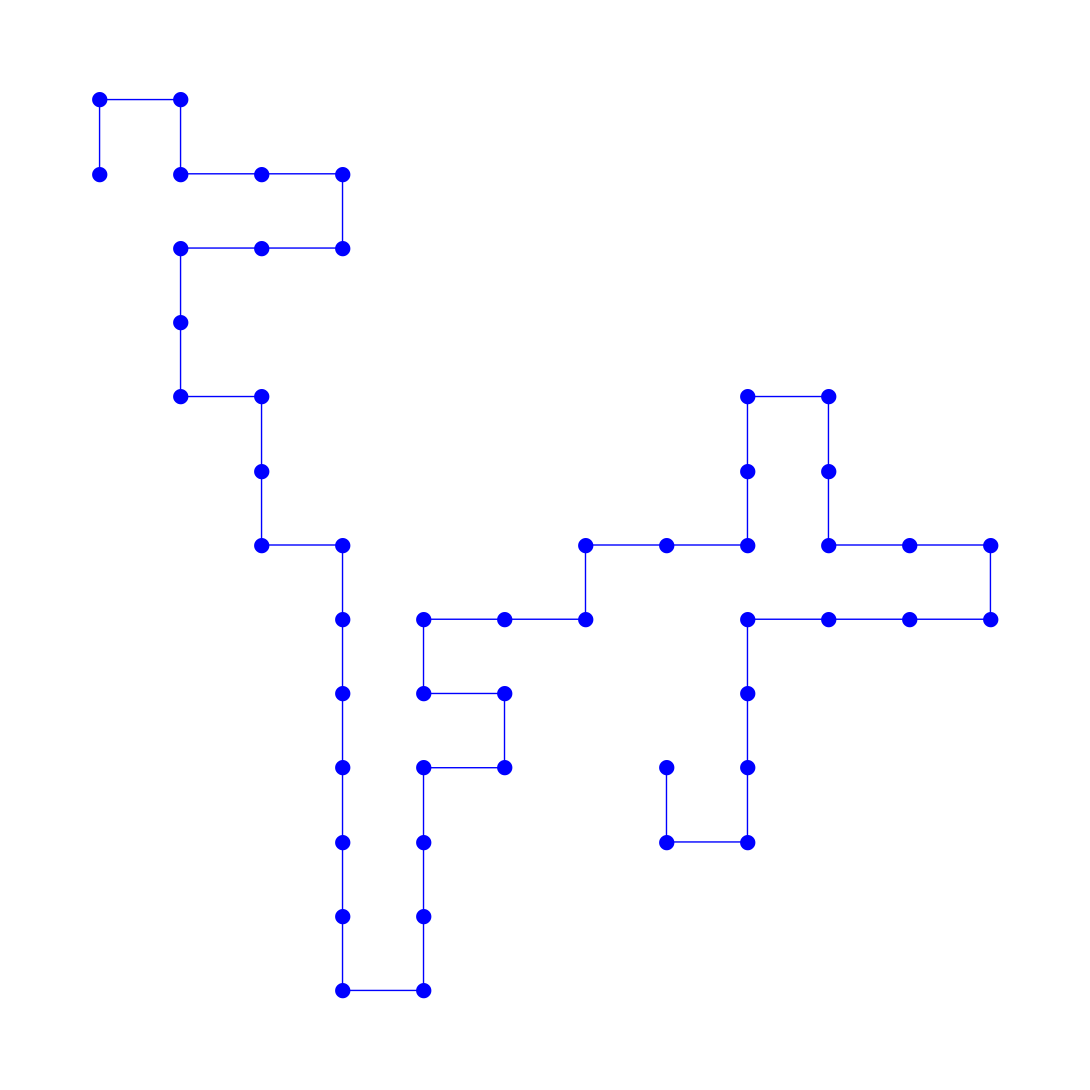

```mathematica
ListPlot[UnOccSites00,Joined->True,PlotMarkers->{●,20},PlotStyle->Blue,Axes->False,AspectRatio->1]
```

```mathematica
(*chain length 50, saturation fraction 1*)
```

```mathematica
linpolyedgelist={1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,11<->12,12<->13,13<->14,14<->15,15<->16,16<->17,17<->18,18<->19,19<->20,20<->21,21<->22,22<->23,23<->24,24<->25,25<->26,26<->27,27<->28,28<->29,29<->30,30<->31,31<->32,32<->33,33<->34,34<->35,35<->36,36<->37,37<->38,38<->39,39<->40,40<->41,41<->42,42<->43,43<->44,44<->45,45<->46,46<->47,47<->48,48<->49,49<->50};
```

```mathematica
polyconfig={{{0,0},1},{{-1,0},1},{{-1,1},1},{{0,1},1},{{1,1},1},{{1,0},1},{{1,-1},1},{{0,-1},1},{{-1,-1},1},{{-1,-2},1},{{-2,-2},1},{{-2,-1},1},{{-2,0},1},{{-2,1},1},{{-2,2},1},{{-1,2},1},{{0,2},1},{{1,2},1},{{1,3},1},{{0,3},1},{{-1,3},1},{{-2,3},1},{{-2,4},1},{{-1,4},1},{{0,4},1},{{1,4},1},{{2,4},1},{{2,3},1},{{2,2},1},{{2,1},1},{{2,0},1},{{2,-1},1},{{2,-2},1},{{1,-2},1},{{0,-2},1},{{0,-3},1},{{-1,-3},1},{{-1,-4},1},{{0,-4},1},{{1,-4},1},{{1,-3},1},{{2,-3},1},{{2,-4},1},{{2,-5},1},{{1,-5},1},{{0,-5},1},{{-1,-5},1},{{-2,-5},1},{{-2,-4},1},{{-2,-3},1}};
```

```mathematica
vcoors={{0,0},{-1,0},{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1},{-1,-1},{-1,-2},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-1,2},{0,2},{1,2},{1,3},{0,3},{-1,3},{-2,3},{-2,4},{-1,4},{0,4},{1,4},{2,4},{2,3},{2,2},{2,1},{2,0},{2,-1},{2,-2},{1,-2},{0,-2},{0,-3},{-1,-3},{-1,-4},{0,-4},{1,-4},{1,-3},{2,-3},{2,-4},{2,-5},{1,-5},{0,-5},{-1,-5},{-2,-5},{-2,-4},{-2,-3}};
```

```mathematica
vocc=Range[1,50];
```

```mathematica
linpolygraph50with50=Graph[linpolyedgelist,VertexCoordinates->vcoors,VertexSize->Large,EdgeStyle->Thickness[0.02]];
```

```mathematica
HighlightGraph[linpolygraph50with50,Style[vocc,Darker[Red]]]
```

```mathematica
Length[polyconfig]
```

50

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
OccSites={}
```

{}

```mathematica
Do[
Coor=polyconfig[[posn,1]];
OccSites=Append[OccSites,Coor];
,{posn,OccPosns}];
```

```mathematica
Length[OccSites]
```

```mathematica
50
OccSites10=OccSites
```

50

{{0,0},{-1,0},{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1},{-1,-1},{-1,-2},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-1,2},{0,2},{1,2},{1,3},{0,3},{-1,3},{-2,3},{-2,4},{-1,4},{0,4},{1,4},{2,4},{2,3},{2,2},{2,1},{2,0},{2,-1},{2,-2},{1,-2},{0,-2},{0,-3},{-1,-3},{-1,-4},{0,-4},{1,-4},{1,-3},{2,-3},{2,-4},{2,-5},{1,-5},{0,-5},{-1,-5},{-2,-5},{-2,-4},{-2,-3}}

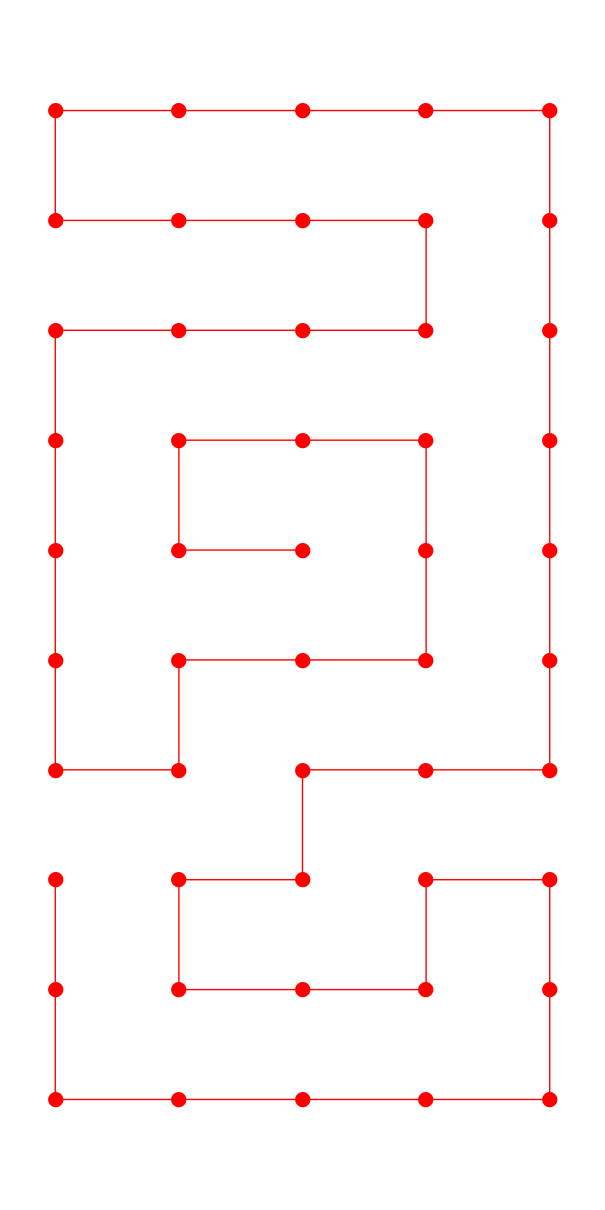

```mathematica
ListPlot[OccSites10,Joined->True,PlotMarkers->{●,20},PlotStyle->Red,Axes->False,AspectRatio->1/0.5]
```

```mathematica
testlist=Import["/home/singaram/data/rosenbluth/linear/comp_exp/150vs75/RAWRBFactor_123_150.txt","List"]
```

{1.34504×10^195,1.32433×10^188,2.84876×10^203,1.66176×10^194,6.10092×10^193}

```mathematica
tot=Total[testlist]
```

2.84876×10^203

```mathematica
testlist/tot
```

{4.72151×10^-9,4.6488×10^-16,1.,5.83328×10^-10,2.14161×10^-10}

```mathematica
(*ok, now to config select script to select which line we read in and we'll use shell functions embedded in mathematica*)
```

```mathematica
NumberQ[1.354*10^195]
```

True

```mathematica
NumberQ[N[First[testlist]]]
```

False

```mathematica
branchedpolyconfig={{{0,0},1},{{0,1},1},{{-1,1},1},{{-1,0},1},{{-1,2},1},{{-2,1},0},{{-3,1},0},{{-3,0},1},{{-2,0},1},{{-4,0},1},{{-3,2},0},{{-4,1},0}}
```

{{{0,0},1},{{0,1},1},{{-1,1},1},{{-1,0},1},{{-1,2},1},{{-2,1},0},{{-3,1},0},{{-3,0},1},{{-2,0},1},{{-4,0},1},{{-3,2},0},{{-4,1},0}}

```mathematica
Length[branchedpoly]
```

12

```mathematica
OccUnOccList=OccUnOccPosns[branchedpolyconfig]
```

{{1,2,3,4,5,8,9,10},{6,7,11,12}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{1,2,3,4,5,8,9,10}

```mathematica
UnOccPosns=OccUnOccList[[2]]
```

{6,7,11,12}

```mathematica
OccSites={}
```

{}

```mathematica
Do[
Coor=branchedpolyconfig[[posn,1]];
OccSites=Append[OccSites,Coor];
,{posn,OccPosns}];
```

```mathematica
OccSites
```

{{0,0},{0,1},{-1,1},{-1,0},{-1,2},{-3,0},{-2,0},{-4,0}}

```mathematica
UnOccSites={}
```

{}

```mathematica
Do[
Coor=branchedpolyconfig[[posn,1]];
UnOccSites=Append[UnOccSites,Coor];
,{posn,UnOccPosns}];
```

```mathematica
UnOccSites
```

{{-2,1},{-3,1},{-3,2},{-4,1}}

```mathematica
OccSitesBranched=OccSites;
```

```mathematica
UnOccSitesBranched=UnOccSites;
```

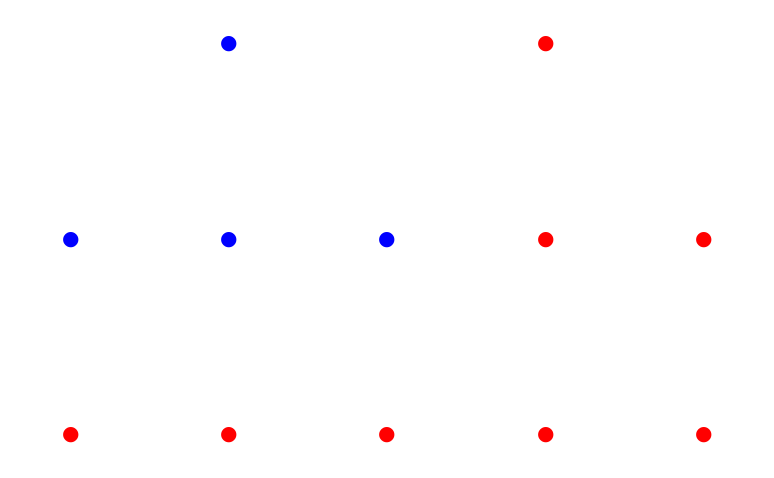

```mathematica
ListPlot[{UnOccSitesBranched,OccSitesBranched},Joined->{False,False},PlotMarkers->{{●,20},{●,20}},PlotStyle->{Blue,Red},Axes->False]
```

```mathematica
rnaasgraph=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[3,5],UndirectedEdge[3,6],UndirectedEdge[6,7],UndirectedEdge[7,8],UndirectedEdge[8,9],UndirectedEdge[8,10],UndirectedEdge[7,11],UndirectedEdge[7,12]},VertexCoordinates->vcoors,VertexLabels->"Name"]
```

-Graphics-

```mathematica
HighlightGraph[rnaasgraph,Subgraph[rnaasgraph,OccPosns]]
```

```mathematica
VertexList[rnaasgraph]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
AdjacencyMatrix[rnaasgraph]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
vcoors=ConstantArray[0,12]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vcoors[[1]]={1,2}
```

{1,2}

```mathematica
vcoors
```

{{1,2},0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Do[
vcoors[[OccPosns[[i]]]]=OccSites[[i]];

,{i,8}]
```

```mathematica
vcoors
```

{{0,0},{0,1},{-1,1},{-1,0},{-1,2},0,0,{-3,0},{-2,0},{-4,0},0,0}

```mathematica
Do[
vcoors[[UnOccPosns[[i]]]]=UnOccSites[[i]];

,{i,4}]
```

```mathematica
vcoors
```

{{0,0},{0,1},{-1,1},{-1,0},{-1,2},{-2,1},{-3,1},{-3,0},{-2,0},{-4,0},{-3,2},{-4,1}}

```mathematica
graph=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[3,5],UndirectedEdge[3,6],UndirectedEdge[6,7],UndirectedEdge[7,8],UndirectedEdge[8,9],UndirectedEdge[8,10],UndirectedEdge[7,11],UndirectedEdge[7,12]},VertexLabels->"Name"]
```

```mathematica
b11500=Import["~/data/tree-graph_models/lapmats/B1_1500.lap","Table"];
```

```mathematica
graph1500nt=AdjacencyGraph[b11500,GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
Sort[VertexDegree[graph1500nt]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4}

```mathematica
branchedpolyconfig1500={{{0,0},0},{{0,1},0},{{-1,1},0},{{-1,2},0},{{1,0},0},{{2,0},0},{{2,1},0},{{3,1},0},{{3,2},0},{{4,2},0},{{3,0},0},{{4,0},0},{{4,1},0},{{5,1},0},{{1,1},0},{{2,2},0},{{1,2},0},{{2,-1},0},{{2,-2},0},{{2,-3},0},{{2,-4},0},{{2,-5},0},{{2,-6},0},{{3,-5},0},{{1,-5},0},{{1,-4},0},{{1,-6},0},{{1,-7},0},{{2,-7},0},{{3,-7},0},{{3,-6},0},{{2,-8},0},{{3,-8},0},{{2,-9},0},{{3,-9},0},{{4,-9},0},{{4,-8},0},{{5,-8},0},{{6,-8},0},{{2,-10},0},{{1,-10},0},{{2,-11},0},{{3,-11},0},{{4,-11},0},{{1,-11},0},{{1,-12},0},{{0,-11},0},{{2,-12},0},{{2,-13},0},{{1,-13},0},{{1,-14},0},{{2,-14},0},{{3,-12},0},{{4,-12},0},{{1,-8},0},{{1,-9},0},{{0,-9},0},{{0,-6},0},{{0,-5},0},{{0,-4},0},{{0,-3},0},{{-1,-3},0},{{-1,-4},0},{{-2,-4},0},{{-2,-3},0},{{1,-3},0},{{1,-2},0},{{0,-7},0},{{-1,-6},0},{{-1,-5},0},{{-2,-5},0},{{3,-2},0},{{3,-3},0},{{1,-1},0},{{0,-1},0},{{-1,-1},0}};
```

```mathematica
Length[branchedpolyconfig1500]
```

76

```mathematica
OccUnOccList=OccUnOccPosns[branchedpolyconfig1500]
```

{{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76}}

```mathematica
UnOccPosns=OccUnOccList[[2]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76}

```mathematica
vcoors=ConstantArray[0,76]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
UnOccSites={}
```

{}

```mathematica
Do[
Coor=branchedpolyconfig1500[[posn,1]];
UnOccSites=Append[UnOccSites,Coor];
,{posn,UnOccPosns}];
```

```mathematica
UnOccSites
```

{{0,0},{0,1},{-1,1},{-1,2},{1,0},{2,0},{2,1},{3,1},{3,2},{4,2},{3,0},{4,0},{4,1},{5,1},{1,1},{2,2},{1,2},{2,-1},{2,-2},{2,-3},{2,-4},{2,-5},{2,-6},{3,-5},{1,-5},{1,-4},{1,-6},{1,-7},{2,-7},{3,-7},{3,-6},{2,-8},{3,-8},{2,-9},{3,-9},{4,-9},{4,-8},{5,-8},{6,-8},{2,-10},{1,-10},{2,-11},{3,-11},{4,-11},{1,-11},{1,-12},{0,-11},{2,-12},{2,-13},{1,-13},{1,-14},{2,-14},{3,-12},{4,-12},{1,-8},{1,-9},{0,-9},{0,-6},{0,-5},{0,-4},{0,-3},{-1,-3},{-1,-4},{-2,-4},{-2,-3},{1,-3},{1,-2},{0,-7},{-1,-6},{-1,-5},{-2,-5},{3,-2},{3,-3},{1,-1},{0,-1},{-1,-1}}

```mathematica
AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexCoordinates->UnOccSites,VertexLabels->"Name"]
```

-Graphics-

```mathematica
branchedpolyconfig1500halfcovered={{{0,0},1},{{-1,0},1},{{-1,-1},1},{{0,-1},1},{{1,0},1},{{1,-1},1},{{2,-1},1},{{2,0},1},{{3,0},1},{{4,0},1},{{2,1},1},{{3,1},1},{{4,1},1},{{4,2},1},{{3,-1},1},{{2,-2},1},{{2,-3},1},{{1,-2},1},{{1,-3},1},{{1,-4},1},{{2,-4},1},{{3,-4},1},{{3,-3},1},{{4,-4},1},{{3,-5},1},{{2,-5},1},{{4,-5},1},{{5,-5},0},{{5,-4},1},{{6,-4},1},{{7,-4},1},{{5,-3},1},{{4,-3},1},{{6,-3},1},{{7,-3},1},{{8,-3},0},{{8,-4},0},{{8,-5},0},{{7,-5},0},{{6,-2},0},{{5,-2},0},{{6,-1},0},{{5,-1},0},{{4,-1},0},{{6,0},0},{{7,0},0},{{5,0},0},{{7,-1},0},{{8,-1},0},{{9,-1},0},{{9,-2},0},{{9,-3},0},{{7,-2},0},{{8,-2},0},{{6,-5},0},{{6,-6},0},{{7,-6},0},{{4,-6},0},{{3,-6},0},{{3,-7},0},{{2,-7},0},{{2,-8},0},{{3,-8},0},{{4,-8},0},{{5,-8},0},{{1,-7},0},{{1,-6},0},{{4,-7},0},{{5,-6},0},{{5,-7},0},{{6,-7},0},{{0,-3},0},{{-1,-3},0},{{0,-2},0},{{-1,-2},0},{{-2,-2},0}};
```

```mathematica
OccUnOccList=OccUnOccPosns[branchedpolyconfig1500halfcovered]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,31,32,33,34,35},{28,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30,31,32,33,34,35}

```mathematica
vcoors={}
```

{}

```mathematica
Do[
Coor=branchedpolyconfig1500halfcovered[[posn,1]];
vcoors=Append[vcoors,Coor];
,{posn,1,76}];
```

```mathematica
vcoors1500halfcovered=vcoors
```

{{0,0},{-1,0},{-1,-1},{0,-1},{1,0},{1,-1},{2,-1},{2,0},{3,0},{4,0},{2,1},{3,1},{4,1},{4,2},{3,-1},{2,-2},{2,-3},{1,-2},{1,-3},{1,-4},{2,-4},{3,-4},{3,-3},{4,-4},{3,-5},{2,-5},{4,-5},{5,-5},{5,-4},{6,-4},{7,-4},{5,-3},{4,-3},{6,-3},{7,-3},{8,-3},{8,-4},{8,-5},{7,-5},{6,-2},{5,-2},{6,-1},{5,-1},{4,-1},{6,0},{7,0},{5,0},{7,-1},{8,-1},{9,-1},{9,-2},{9,-3},{7,-2},{8,-2},{6,-5},{6,-6},{7,-6},{4,-6},{3,-6},{3,-7},{2,-7},{2,-8},{3,-8},{4,-8},{5,-8},{1,-7},{1,-6},{4,-7},{5,-6},{5,-7},{6,-7},{0,-3},{-1,-3},{0,-2},{-1,-2},{-2,-2}}

```mathematica
b1500halfcoveredgraph=AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors1500halfcovered,VertexLabels->"Name"];
```

```mathematica
HighlightGraph[b1500halfcoveredgraph,Subgraph[b1500halfcoveredgraph,OccPosns]]
```

-Graphics-

```mathematica
polyconfig500={{{0,0},0},{{0,-1},0},{{1,-1},0},{{2,-1},0},{{3,-1},0},{{4,-1},0},{{4,-2},0},{{5,-1},0},{{5,0},0},{{5,1},0},{{4,1},0},{{3,1},0},{{6,1},0},{{6,2},0},{{7,2},0},{{7,3},0},{{6,0},0},{{4,0},0},{{3,0},0},{{3,-2},0},{{3,-3},0},{{2,-3},0},{{1,-3},0},{{2,-4},0},{{3,-4},0},{{3,-5},0},{{1,0},0},{{2,0},0},{{2,1},0},{{1,1},0},{{1,2},0}};
```

```mathematica
Length[polyconfig500]
```

31

```mathematica
b1500=Import["~/data/tree-graph_models/lapmats/B1_500.lap","Table"];
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig500]
```

{{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}}

```mathematica
UnOccSites=OccUnOccList[[2]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig500[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,31}];
```

```mathematica
vcoors
```

{{0,0},{0,-1},{1,-1},{2,-1},{3,-1},{4,-1},{4,-2},{5,-1},{5,0},{5,1},{4,1},{3,1},{6,1},{6,2},{7,2},{7,3},{6,0},{4,0},{3,0},{3,-2},{3,-3},{2,-3},{1,-3},{2,-4},{3,-4},{3,-5},{1,0},{2,0},{2,1},{1,1},{1,2}}

```mathematica
AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"]
```

```mathematica
(*B1-500nt representation*)
```

```mathematica
b1000=Import["~/data/tree-graph_models/lapmats/B1_1000.lap","Table"];
```

```mathematica
polyconfig1000={{{0,0},0},{{-1,0},0},{{-2,0},0},{{-3,0},0},{{-1,1},0},{{-2,1},0},{{-3,1},0},{{-4,1},0},{{-5,1},0},{{-5,0},0},{{-4,0},0},{{-4,-1},0},{{-3,-1},0},{{-2,-1},0},{{-2,-2},0},{{-1,-2},0},{{-3,-2},0},{{-3,-3},0},{{-2,-3},0},{{-1,-3},0},{{0,-3},0},{{0,-2},0},{{1,-2},0},{{1,-3},0},{{2,-3},0},{{2,-4},0},{{3,-4},0},{{3,-3},0},{{1,-4},0},{{0,-1},0},{{1,-1},0},{{2,-1},0},{{3,-1},0},{{3,-2},0},{{4,-2},0},{{5,-2},0},{{5,-3},0},{{4,-3},0},{{4,-1},0},{{1,0},0},{{2,0},0},{{3,0},0},{{-4,-3},0},{{-2,2},0},{{0,1},0},{{0,2},0},{{-1,2},0},{{-1,3},0},{{0,3},0},{{0,4},0},{{0,5},0},{{-1,4},0}};
```

```mathematica
Length[polyconfig1000]
```

52

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig1000]
```

{{},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}}

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig1000[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,52}];
```

```mathematica
AdjacencyGraph[b1000,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"]
```

```mathematica
(*B1 1000 nt representation*)
```

```mathematica
(*configuration of 500 nt @ -1 kT, 28 sites occupied*)
```

```mathematica
polyconfig500={{{0,0},0},{{0,-1},1},{{0,-2},1},{{1,-2},1},{{2,-2},1},{{2,-1},1},{{1,-1},1},{{2,0},1},{{3,0},1},{{3,1},1},{{2,1},1},{{1,1},1},{{3,2},1},{{2,2},1},{{1,2},1},{{1,3},1},{{3,-1},1},{{4,0},1},{{4,1},1},{{3,-2},1},{{3,-3},1},{{2,-3},1},{{2,-4},1},{{1,-3},1},{{1,-4},1},{{0,-4},1},{{-1,-2},1},{{-1,-3},0},{{0,-3},1},{{-1,-1},1},{{-2,-1},0}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig500]
```

{{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30},{1,28,31}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29,30}

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig500[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,31}];
```

```mathematica
b1500graph=AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"]
```

```mathematica
HighlightGraph[b1500graph,Subgraph[b1500graph,OccPosns]]
```

-Graphics-

```mathematica
(*ok, let's checkout what 28 proteins on the 1000nt RNA would look like*)
```

```mathematica
polyconfig1000={{{0,0},0},{{0,-1},0},{{-1,-1},1},{{-1,0},0},{{0,-2},1},{{-1,-2},1},{{-1,-3},0},{{0,-3},1},{{1,-3},1},{{2,-3},0},{{0,-4},0},{{1,-4},1},{{1,-5},1},{{2,-5},0},{{3,-5},1},{{3,-4},1},{{0,-5},1},{{0,-6},1},{{0,-7},1},{{1,-7},1},{{1,-8},0},{{0,-8},0},{{-1,-8},1},{{-1,-7},1},{{-1,-6},1},{{-2,-6},0},{{-3,-6},0},{{-1,-5},1},{{-2,-7},0},{{0,-9},1},{{0,-10},1},{{1,-10},1},{{2,-10},0},{{2,-9},0},{{2,-8},0},{{2,-7},1},{{3,-7},1},{{3,-6},1},{{2,-11},0},{{-1,-10},1},{{-1,-9},1},{{-2,-9},0},{{1,-6},0},{{-2,-2},1},{{1,-2},0},{{1,-1},1},{{2,-1},0},{{3,-1},0},{{1,0},1},{{1,1},0},{{0,1},0},{{1,2},0}};
```

```mathematica
Length[polyconfig1000]
```

52

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig1000]
```

{{3,5,6,8,9,12,13,15,16,17,18,19,20,23,24,25,28,30,31,32,36,37,38,40,41,44,46,49},{1,2,4,7,10,11,14,21,22,26,27,29,33,34,35,39,42,43,45,47,48,50,51,52}}

```mathematica
OccPosns=OccUnOccList[[1]];
```

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig1000[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,52}];
```

```mathematica
Length[vcoors]
```

52

```mathematica
Sort[VertexDegree[b11000graph]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Sort[VertexDegree[b1500graph]]
```

{1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4}

```mathematica
b11000graph=AdjacencyGraph[b1000,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"]
```

```mathematica
HighlightGraph[b11000graph,Subgraph[b11000graph,OccPosns]]
```

-Graphics-

```mathematica
(*let's look at pictures of 500 nt and 1000 nt RNA at -3kT*)
```

```mathematica
(*here is the 1000 nt*)
polyconfig1000={{{0,0},1},{{1,0},1},{{2,0},1},{{2,1},1},{{1,1},1},{{0,1},1},{{-1,1},1},{{-2,1},1},{{-2,0},1},{{-1,0},1},{{-3,1},1},{{-3,0},1},{{-4,0},1},{{-4,1},1},{{-4,2},1},{{-3,2},1},{{-4,-1},1},{{-3,-1},1},{{-2,-1},1},{{-1,-1},1},{{0,-1},1},{{1,-1},1},{{2,-1},1},{{3,-1},1},{{3,0},1},{{3,1},1},{{3,2},1},{{4,0},0},{{3,-2},1},{{1,-2},0},{{1,-3},0},{{1,-4},0},{{0,-4},0},{{0,-3},0},{{0,-2},0},{{-1,-2},0},{{-1,-3},0},{{-1,-4},0},{{0,-5},0},{{2,-3},0},{{2,-4},0},{{3,-4},0},{{-3,-2},0},{{0,2},0},{{1,2},0},{{1,3},0},{{1,4},0},{{0,4},0},{{0,3},0},{{-1,3},0},{{-2,3},0},{{-1,4},0}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig1000]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29},{28,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}}

```mathematica
OccPosns=OccUnOccList[[1]];
```

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig1000[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,52}];
```

```mathematica
b11000graph=AdjacencyGraph[b1000,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"];
```

```mathematica
HighlightGraph[b11000graph,Subgraph[b11000graph,OccPosns]]
```

-Graphics-

```mathematica
(*now let's look at 500 nt with 28 protein*)
```

```mathematica
polyconfig500={{{0,0},1},{{1,0},1},{{2,0},1},{{3,0},1},{{3,-1},1},{{2,-1},1},{{1,-1},1},{{2,-2},1},{{2,-3},1},{{1,-3},1},{{1,-2},1},{{0,-2},1},{{0,-3},1},{{-1,-3},1},{{-2,-3},1},{{-3,-3},1},{{2,-4},1},{{3,-3},1},{{3,-2},1},{{4,-1},1},{{4,-2},1},{{4,-3},1},{{5,-3},1},{{4,-4},1},{{3,-4},1},{{3,-5},1},{{2,1},0},{{3,1},1},{{4,1},1},{{2,2},0},{{2,3},0}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig500]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29},{27,30,31}}

```mathematica
OccPosns=OccUnOccList[[1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29}

```mathematica
vcoors={};
```

```mathematica
Do[
Coor=polyconfig500[[i,1]];
vcoors=Append[vcoors,Coor];
,{i,1,31}];
```

```mathematica
b1500graph=AdjacencyGraph[b1500,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors,VertexLabels->"Name"];
```

```mathematica
HighlightGraph[b1500graph,Subgraph[b1500graph,OccPosns]]
```

-Graphics-

```mathematica
(*modified 500nt graph*)
```

```mathematica
adjgraph500mod=AdjacencyGraph[b1500,VertexLabels->"Name"]
```

-Graphics-

```mathematica
adjgraph500mod=EdgeAdd[adjgraph500mod,{17<->16,1<->7}]
```

-Graphics-

```mathematica
adjgraph500mod=EdgeDelete[adjgraph500mod,{17<->9,7<->6}]
```

-Graphics-

```mathematica
Export["/home/singaram/adjmat500mod.dat",AdjacencyMatrix[adjgraph500mod],"Table"]
```

/home/singaram/adjmat500mod.dat

```mathematica
adjmattset=Import["/home/singaram/adjmat500mod.dat","Table"];
```

```mathematica
Dimensions[adjmattset]
```

{31,31}

```mathematica
AdjacencyGraph[AdjacencyMatrix[adjgraph500mod],GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
(*now modify 1000 nt graph*)
adjgraph1000mod=AdjacencyGraph[b1000,VertexLabels->"Name"]
```

-Graphics-

```mathematica
adjgraph1000mod=EdgeAdd[adjgraph1000mod,{45<->12,34<->17}]
```

-Graphics-

```mathematica
adjgraph1000mod=EdgeDelete[adjgraph1000mod,{45<->5,34<->33}]
```

-Graphics-

```mathematica
Export["/home/singaram/adjmat1000mod.dat",AdjacencyMatrix[adjgraph1000mod],"Table"]
```

/home/singaram/adjmat1000mod.dat

```mathematica
Emin=ConstantArray[0,52];
```

```mathematica
frac1000=ConstantArray[0,52]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*computed fraction of proteins on 1000 nt by finding the minimum average energy*)
(*this is 1000 nt vs 500 nt*)
```

```mathematica
Do[
Elist=ConstantArray[0,i+1];
(*there are i proteins in total, j-1 is how many proteins are on 1000 nt*)
Do[
If[j== (i+1) || j==1,
If[ j==1,
If[i >31,
(*cannot place proteins on 500nt *)

,
Elist[[j]]=aveenergy500[[i]];];
,
Elist[[j]]=aveenergy1000[[i]];
 ];
,
If[i+1-j > 31,
(*cannot place proteins on 500 nt, this configuration is not possible*)

,
Elist[[j]]=aveenergy1000[[j-1]]+aveenergy500[[i+1-j]];];

    ];
,{j,1,i+1}];

(*position in Elist of the energy minimum, this corresponds to the number of protein on 1000 nt*)
numprot=Position[Elist,Min[Elist]][[1,1]]-1;
Print[{numprot,Elist}];
Emin[[i]]=Min[Elist];
frac1000[[i]]=N[numprot/i];

,{i,1,52}];
```

```mathematica
aveenergy1000[[21]]
```

-94.1723

```mathematica
aveenergy500[[31]]
```

-143.097

```mathematica
frac1000
```

{0.5,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.0909091,0.,0.,1.,0.,0.,0.0588235,1.,1.,0.,1.,0.954545,1.,1.,1.,1.,1.,0.,0.,0.,1.,0.96875,1.,0.970588,1.,0.972222,1.,1.,1.,1.,0.804878,1.,0.813953,1.,1.,0.978261,1.,1.,1.,0.9,1.,0.980769}

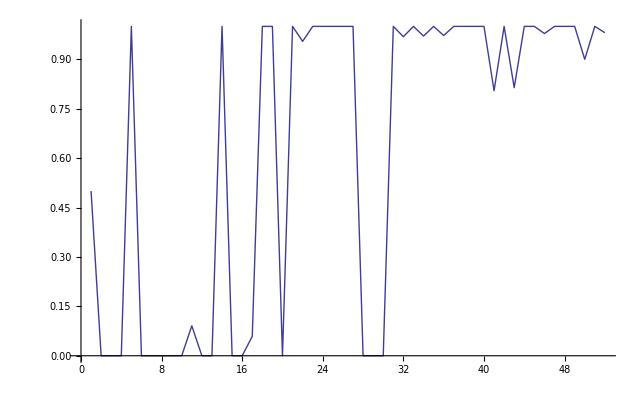

```mathematica
ListPlot[frac1000,Joined->True]
```

```mathematica
Export["/home/singaram/frac1000vs500.dat",frac1000,"Table"]
```

/home/singaram/frac1000vs500.dat

```mathematica
{0,-2.75157,-5.60241,-8.47983,-12.5172,-17.1842,-21.999,-29.8743,-30.5345,-36.4842,-36.4842,-41.557,-50.973,-57.6207,-61.1467,-68.9802,-68.9802,-75.6389,-76.1983,-84.2334,-94.1723,-94.1723,-99.2729,-102.04,-114.164,-115.01,-119.972,-126.198,-131.892,-140.998,-146.997,-146.997,-161.701,-161.701,-169.097,-169.097,-175.576,-182.813,-185.422,-187.475,-191.5753,-197.988,-198.9713,-206.412,-221.929,-221.929,-227.05,-230.83,-230.998,-233.8866,-249.066,-249.066}
```

```mathematica
(*minimum average energy*)
```

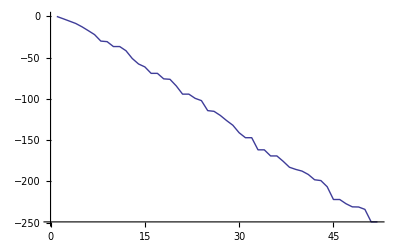

```mathematica
ListPlot[Emin,Joined->True]
```

```mathematica
(*from Ajay's paper I got the degree distribution for B3*)
(*I made a smaller tree with 33 vertices (~1/4 the size of B3) with the same degree distribution*)
```

```mathematica
i=0
```

0

```mathematica
While[ i < 1,
A=RandomGraph[DegreeGraphDistribution[Reverse[{1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4}]]];
            If[ConnectedGraphQ[A],
                       B=A;
                       i=2;
                 ];
         ];
```

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
MinimumBandwidthOrdering[B]
```

{28,18,32,21,15,30,8,6,33,19,5,12,17,3,26,13,7,22,31,1,11,24,14,20,27,2,29,4,10,9,23,16,25}

Graph[{28,18,32,21,15,30,8,6,33,19,5,12,17,3,26,13,7,22,31,1,11,24,14,20,27,2,29,4,10,9,23,16,25},VertexLabels→Name]

```mathematica
B333v=Graph[{33<->25,26<->28,22<->27,21<->3,19<->20,33<->18,30<->24,30<->15,31<->27,13<->28,22<->32,33<->20,6<->26,7<->16,12<->13,30<->11,27<->21,32<->17,8<->15,29<->33,12<->9,31<->23,1<->14,25<->2,31<->14,16<->17,28<->24,10<->29,29<->4,18<->32,19<->11,5<->23},VertexLabels->"Name",GraphLayout->"SpringEmbedding"]
```

-Graphics-

```mathematica
Graph[TopologicalSort@B333v,EdgeList@B333v]
```

Graph[TopologicalSort[-Graphics-],{33<->25,26<->28,22<->27,21<->3,19<->20,33<->18,30<->24,30<->15,31<->27,13<->28,22<->32,33<->20,6<->26,7<->16,12<->13,30<->11,27<->21,32<->17,8<->15,29<->33,12<->9,31<->23,1<->14,25<->2,31<->14,16<->17,28<->24,10<->29,29<->4,18<->32,19<->11,5<->23}]

```mathematica
neworder=Thread[MinimumBandwidthOrdering[B333v]->Range[33]]
```

{28→1,33→2,29→3,27→4,15→5,8→6,6→7,7→8,5→9,19→10,17→11,20→12,23→13,11→14,32→15,25→16,1→17,31→18,2→19,10→20,30→21,9→22,24→23,22→24,14→25,12→26,18→27,13→28,3→29,4→30,16→31,21→32,26→33}

```mathematica
DepthFirstScan[B333v,1,{Rule["PrevisitVertex",((vertnum=#1;Print[vertnum];)&)]}];
```

```mathematica
b1500mod=AdjacencyGraph[Import["~/data/tree-graph_models/lapmats/B1_500mod.lap","Table"],VertexLabels->"Name",GraphLayout->"SpringEmbedding"]
```

-Graphics-

```mathematica
b1500modcompact=EdgeAdd[b1500mod,6<->2];
```

```mathematica
b1500modcompact=EdgeDelete[b1500modcompact,2<->3]
```

-Graphics-

```mathematica
Export["~/B1_500modcompact.dat",AdjacencyMatrix[b1500modcompact],"Table"]
```

~/B1_500modcompact.dat

```mathematica
b1500modextended=b1500mod
```

```mathematica
Export["~/b1500modext.dat",AdjacencyMatrix[b1500modextended],"Table"]
```

~/b1500modext.dat

```mathematica
AdjacencyGraph[Import["~/data/tree-graph_models/lapmats/B1_500modcompact.lap","Table"],GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
AdjacencyGraph[Import["~/data/tree-graph_models/lapmats/B1_500modext.lap","Table"],GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
(*import tree graph with 50 vertices whose distribution comes from RNAs with random, but uniform sequences*)
rand50mat=Import["/usr/people/abs/singaram/data/lapmats/rand50.lap","Table"];
```

```mathematica
Dimensions[rand50mat]
```

{50,50}

```mathematica
graph=AdjacencyGraph[rand50mat,GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
BreadthFirstScan[graph,1,{"PrevisitVertex"->(Print["Visiting",#]&)}];
```

```mathematica
Needs["MonteCarloRosenbluthBranchedPolymer`","/usr/people/abs/singaram/scripts/mathematica/packages/MC_Rosenbluth-branchedpoly.m"]
```

```mathematica
(*polymer configuration*)
polyconfig50={{{0,0},0,1},{{0,1},0,2},{{0,2},0,3},{{-1,2},0,4},{{-1,3},0,5},{{0,3},0,6},{{1,3},0,7},{{1,4},1,8},{{2,4},1,9},{{3,4},1,10},{{4,4},1,11},{{4,3},0,12},{{3,3},1,13},{{2,3},1,14},{{2,2},1,15},{{3,2},1,16},{{4,2},1,17},{{5,2},1,18},{{6,2},1,19},{{7,2},1,20},{{7,1},1,21},{{7,0},1,22},{{7,-1},0,23},{{8,-1},0,24},{{8,0},1,25},{{8,1},1,26},{{9,1},1,27},{{9,2},0,28},{{9,3},1,29},{{9,4},1,30},{{9,5},1,31},{{9,6},1,32},{{9,7},0,50},{{10,5},0,49},{{8,4},1,48},{{8,2},1,47},{{9,0},1,46},{{9,-1},1,45},{{6,0},0,44},{{7,3},0,43},{{5,1},0,41},{{5,3},0,42},{{3,1},0,40},{{3,5},0,39},{{1,2},0,38},{{0,4},0,37},{{-2,3},0,35},{{-1,4},0,36},{{1,0},0,33},{{0,-1},0,34}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig50]
```

{{8,9,10,11,13,14,15,16,17,18,19,20,21,22,25,26,27,29,30,31,32,35,36,37,38},{1,2,3,4,5,6,7,12,23,24,28,33,34,39,40,41,42,43,44,45,46,47,48,49,50}}

```mathematica
(*first we need to give each vertex a coordinate*)
(*then make a list of the vertices which are bound by particles*)
```

```mathematica
OccPosns50=OccUnOccList[[1]];
```

```mathematica
Position[polyconfig50,{_,_,44},2]
```

{{39}}

```mathematica
polyconfig[[2,1]]
```

{0,1}

```mathematica
vcoors50={};
```

```mathematica
Do[
posn=Position[polyconfig50,{_,_,i},i][[1,1]];
Coor=polyconfig50[[posn,1]];
vcoors50=Append[vcoors50,Coor];
,{i,1,50}];
```

```mathematica
rand50graph=AdjacencyGraph[rand50mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors50,VertexLabels->"Name",VertexSize->Large,EdgeStyle->Thick]
```

-Graphics-

```mathematica
vcoors50={};
```

```mathematica
(*now get list of vertices which are bound by particles*)
Do[
posn=Position[polyconfig50,{_,_,i},i][[1,1]];
Coor=polyconfig50[[posn,1]];
vcoors50=Append[vcoors50,Coor];
,{i,1,50}];
```

```mathematica
rand50graph=AdjacencyGraph[rand50mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors50,VertexSize->Large,EdgeStyle->Thick]
```

```mathematica
vocc50
```

{{8,9,10,11,13,14,15,16,17,18,19,20,21,22,25,26,27,29,30,31,32,48,47,46,45}}

```mathematica
(*polymer configuration without any bound particles*)
```

```mathematica
polyconfig50={{{0,0},0,1},{{-1,0},0,2},{{-2,0},0,3},{{-3,0},0,4},{{-3,1},0,5},{{-4,1},0,6},{{-4,0},0,7},{{-4,-1},0,8},{{-3,-1},0,9},{{-2,-1},0,10},{{-1,-1},0,11},{{-1,-2},0,12},{{-1,-3},0,13},{{-2,-3},0,14},{{-3,-3},0,15},{{-4,-3},0,16},{{-5,-3},0,17},{{-6,-3},0,18},{{-6,-2},0,19},{{-6,-1},0,20},{{-6,0},0,21},{{-7,0},0,22},{{-7,1},0,23},{{-8,1},0,24},{{-8,0},0,25},{{-9,0},0,26},{{-9,-1},0,27},{{-9,-2},0,28},{{-9,-3},0,29},{{-10,-3},0,30},{{-11,-3},0,31},{{-11,-4},0,32},{{-12,-4},0,50},{{-12,-3},0,49},{{-10,-4},0,48},{{-9,1},0,47},{{-8,-1},0,46},{{-8,2},0,45},{{-7,-1},0,44},{{-5,-1},0,43},{{-7,-3},0,41},{{-6,-4},0,42},{{-4,-4},0,40},{{-2,-2},0,39},{{-5,0},0,38},{{-4,2},0,37},{{-3,2},0,35},{{-2,1},0,36},{{1,0},0,33},{{0,1},0,34}};
```

```mathematica
vcoors50={};
```

```mathematica
HighlightGraph[rand50graph,Subgraph[rand50graph,First[vocc50]]]
```

```mathematica
(*now do the same thing for the 26-vertex graph*)
```

```mathematica
rand26mat=Import["/usr/people/abs/singaram/data/lapmats/rand25.lap","Table"];
```

```mathematica
Dimensions[rand26mat]
```

{26,26}

```mathematica
AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
polyconfig26={{{0,0},0,1},{{0,-1},0,2},{{0,-2},0,3},{{0,-3},0,4},{{-1,-3},0,5},{{-2,-3},0,6},{{-2,-2},1,7},{{-3,-2},1,8},{{-3,-1},1,9},{{-3,0},1,10},{{-4,0},1,11},{{-5,0},1,12},{{-6,0},1,13},{{-6,1},1,14},{{-6,2},0,15},{{-6,3},0,16},{{-5,3},1,25},{{-7,3},0,26},{{-5,1},1,24},{{-5,-1},1,23},{{-2,0},1,21},{{-3,1},1,22},{{-3,-3},0,20},{{-1,-4},0,19},{{-1,0},0,17},{{1,0},0,18}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig26]
```

{{7,8,9,10,11,12,13,14,17,19,20,21,22},{1,2,3,4,5,6,15,16,18,23,24,25,26}}

```mathematica
OccPosns26=OccUnOccList[[1]];
```

```mathematica
(*poly config in the absence of particles*)
polyconfig26={{{0,0},0,1},{{1,0},0,2},{{1,-1},0,3},{{2,-1},0,4},{{2,-2},0,5},{{1,-2},0,6},{{1,-3},0,7},{{2,-3},0,8},{{2,-4},0,9},{{2,-5},0,10},{{3,-5},0,11},{{4,-5},0,12},{{5,-5},0,13},{{5,-4},0,14},{{6,-4},0,15},{{6,-3},0,16},{{7,-3},0,25},{{5,-3},0,26},{{4,-4},0,24},{{4,-6},0,23},{{2,-6},0,21},{{1,-5},0,22},{{3,-3},0,20},{{3,-2},0,19},{{0,1},0,17},{{0,-1},0,18}};
```

```mathematica
vcoors26={};
```

```mathematica
Do[
posn=Position[polyconfig26,{_,_,i},i][[1,1]];
Coor=polyconfig26[[posn,1]];
vcoors26=Append[vcoors26,Coor];
,{i,1,26}];
```

```mathematica
rand26graph=AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors26,VertexSize->Large,EdgeStyle->Thick]
```

```mathematica
vocc26={};
```

```mathematica
Do[
vocc26=Append[vocc26,polyconfig26[[i,3]]];

,{i,{OccPosns26}}];
```

```mathematica
vocc26
```

{{7,8,9,10,11,12,13,14,25,24,23,21,22}}

```mathematica
HighlightGraph[rand26graph,Subgraph[rand26graph,First[vocc26]]]
```

```mathematica
(*now do the final states of the 50 vertex guy and 26*)
```

```mathematica
polyconfig5034={{{0,0},1,1},{{0,-1},1,2},{{-1,-1},1,3},{{-2,-1},1,4},{{-2,-2},1,5},{{-3,-2},1,6},{{-3,-3},0,7},{{-3,-4},0,8},{{-4,-4},1,9},{{-5,-4},1,10},{{-6,-4},1,11},{{-6,-3},1,12},{{-6,-2},0,13},{{-6,-1},0,14},{{-5,-1},1,15},{{-5,0},1,16},{{-5,1},1,17},{{-4,1},1,18},{{-4,2},1,19},{{-5,2},1,20},{{-5,3},0,21},{{-4,3},0,22},{{-3,3},1,23},{{-3,4},1,24},{{-2,4},1,25},{{-2,3},1,26},{{-1,3},1,27},{{-1,4},1,28},{{0,4},1,29},{{0,3},1,30},{{0,2},1,31},{{0,1},1,32},{{-1,1},1,50},{{-1,2},1,49},{{1,3},1,48},{{-2,2},1,47},{{-2,5},1,46},{{-3,5},1,45},{{-4,4},1,44},{{-6,2},0,43},{{-4,0},1,41},{{-3,1},0,42},{{-6,0},0,40},{{-5,-3},0,39},{{-4,-3},0,38},{{-3,-1},0,37},{{-2,-3},0,35},{{-1,-2},0,36},{{1,0},0,33},{{-1,0},0,34}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig5034];
```

```mathematica
OccPosns5034=OccUnOccList[[1]];
```

```mathematica
vcoors5034={};
```

```mathematica
Do[
posn=Position[polyconfig5034,{_,_,i},i][[1,1]];
Coor=polyconfig5034[[posn,1]];
vcoors5034=Append[vcoors5034,Coor];
,{i,1,50}];
```

```mathematica
rand5034graph=AdjacencyGraph[rand50mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors5034,VertexLabels->"Name",VertexSize->Large,EdgeStyle->Thick];
```

```mathematica
vocc5034={};
```

```mathematica
Do[
vocc5034=Append[vocc5034,polyconfig5034[[i,3]]];
,{i,{OccPosns5034}}];
```

```mathematica
HighlightGraph[rand5034graph,Subgraph[rand5034graph,First[vocc5034]]]
```

```mathematica
polyconfig2604={{{0,0},0,1},{{0,1},0,2},{{1,1},0,3},{{2,1},0,4},{{3,1},1,5},{{4,1},0,6},{{4,2},0,7},{{5,2},0,8},{{5,1},0,9},{{5,0},0,10},{{5,-1},0,11},{{5,-2},1,12},{{5,-3},0,13},{{6,-3},0,14},{{6,-4},0,15},{{7,-4},0,16},{{8,-4},1,25},{{7,-5},0,26},{{7,-3},0,24},{{6,-2},0,23},{{4,0},0,21},{{6,0},1,22},{{5,3},0,20},{{3,0},0,19},{{0,-1},0,17},{{-1,0},0,18}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig2604];
```

```mathematica
OccPosns2604=OccUnOccList[[1]];
```

```mathematica
vcoors2604={};
```

```mathematica
Do[
posn=Position[polyconfig2604,{_,_,i},i][[1,1]];
Coor=polyconfig2604[[posn,1]];
vcoors2604=Append[vcoors2604,Coor];
,{i,1,26}];
```

```mathematica
rand2604graph=AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors2604,VertexLabels->"Name",VertexSize->Large,EdgeStyle->Thick];
```

```mathematica
vocc2604={};
```

```mathematica
Do[
vocc2604=Append[vocc2604,polyconfig2604[[i,3]]];
,{i,{OccPosns2604}}];
```

```mathematica
HighlightGraph[rand2604graph,Subgraph[rand2604graph,First[vocc2604]]]
```

```mathematica
polyconfig5050={{{0,0},1,1},{{0,-1},1,2},{{0,-2},1,3},{{0,-3},1,4},{{-1,-3},1,5},{{-1,-2},1,6},{{-1,-1},1,7},{{-1,0},1,8},{{-2,0},1,9},{{-2,1},1,10},{{-2,2},1,11},{{-3,2},1,12},{{-3,1},1,13},{{-3,0},1,14},{{-4,0},1,15},{{-4,1},1,16},{{-4,2},1,17},{{-4,3},1,18},{{-3,3},1,19},{{-2,3},1,20},{{-1,3},1,21},{{0,3},1,22},{{1,3},1,23},{{1,4},1,24},{{0,4},1,25},{{0,5},1,26},{{0,6},1,27},{{-1,6},1,28},{{-1,7},1,29},{{0,7},1,30},{{1,7},1,31},{{1,6},1,32},{{1,5},1,50},{{2,7},1,49},{{0,8},1,48},{{-1,5},1,47},{{-1,4},1,46},{{2,4},1,45},{{0,2},1,44},{{-2,4},1,43},{{-4,4},1,41},{{-5,3},1,42},{{-5,1},1,40},{{-1,1},1,39},{{-2,-1},1,38},{{-2,-2},1,37},{{-2,-3},1,35},{{-1,-4},1,36},{{0,1},1,33},{{1,0},1,34}};
```

```mathematica
OccUnOccList=OccUnOccPosns[polyconfig5050];
```

```mathematica
OccPosns5050=OccUnOccList[[1]];
```

```mathematica
vcoors5050={};
```

```mathematica
Do[
posn=Position[polyconfig5050,{_,_,i},i][[1,1]];
Coor=polyconfig5050[[posn,1]];
vcoors5050=Append[vcoors5050,Coor];
,{i,1,50}];
```

```mathematica
rand5050graph=AdjacencyGraph[rand50mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors5050,VertexLabels->"Name"];
```

```mathematica
vocc5050={};
```

```mathematica
Do[
vocc5050=Append[vocc5050,polyconfig5050[[i,3]]];
,{i,{OccPosns5050}}];
```

```mathematica
HighlightGraph[rand5050graph,Subgraph[rand5050graph,First[vocc5050]]]
```

```mathematica
(*slightly modified code so I start from any vertex, all these graphs should have the same connectivity*)
```

```mathematica
polyconfig1={{{0,0},0,5},{{0,-1},0,4},{{1,-1},0,3},{{1,0},0,2},{{2,0},0,1},{{1,-2},0,17},{{2,-1},0,18},{{-1,0},0,6},{{-2,0},0,7},{{-3,0},0,8},{{-3,1},0,9},{{-3,2},0,10},{{-4,2},0,11},{{-4,3},0,12},{{-4,4},0,13},{{-4,5},0,14},{{-3,5},0,15},{{-2,5},0,16},{{-2,6},0,25},{{-2,4},0,26},{{-5,5},0,24},{{-5,3},0,23},{{-2,2},0,21},{{-3,3},0,22},{{-3,-1},0,20},{{0,1},0,19}};
```

```mathematica
vcoors1={};
```

```mathematica
Do[
posn=Position[polyconfig1,{_,_,i},i][[1,1]];
Coor=polyconfig1[[posn,1]];
vcoors1=Append[vcoors1,Coor];
,{i,1,26}];
```

```mathematica
rand26mat=Import["/usr/people/abs/singaram/data/lapmats/rand25.lap","Table"];
```

```mathematica
AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

-Graphics-

```mathematica
DepthFirstScan[graph1,5,{"PrevisitVertex"->(Print["Visiting",#]&)}];
```

```mathematica
graph1=AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors1,VertexLabels->"Name"]
```

-Graphics-

```mathematica
polyconfig2={{{0,0},0,23},{{-1,0},0,12},{{-2,0},0,11},{{-2,-1},0,10},{{-2,-2},0,9},{{-3,-2},0,8},{{-4,-2},0,7},{{-4,-3},0,6},{{-4,-4},0,5},{{-4,-5},0,4},{{-4,-6},0,3},{{-4,-7},0,2},{{-4,-8},0,1},{{-3,-8},0,17},{{-5,-8},0,18},{{-5,-4},0,19},{{-3,-3},0,20},{{-1,-1},0,21},{{-3,-1},0,22},{{-1,1},0,13},{{-2,1},0,14},{{-2,2},0,15},{{-3,2},0,16},{{-3,3},0,25},{{-4,2},0,26},{{-3,1},0,24}};
```

```mathematica
vcoors2={};
```

```mathematica
Do[
posn=Position[polyconfig2,{_,_,i},i][[1,1]];
Coor=polyconfig2[[posn,1]];
vcoors2=Append[vcoors2,Coor];
,{i,1,26}];
```

```mathematica
AdjacencyGraph[rand26mat,GraphLayout->"SpringEmbedding",VertexCoordinates->vcoors2,VertexLabels->"Name"]
```

-Graphics-

```mathematica
polyconfig3={{{0,0},0,4},{{0,1},0,3},{{-1,1},0,2},{{-1,2},0,1},{{1,1},0,17},{{0,2},0,18},{{0,-1},0,5},{{0,-2},0,6},{{-1,-2},0,7},{{-2,-2},0,8},{{-3,-2},0,9},{{-4,-2},0,10},{{-5,-2},0,11},{{-5,-1},0,12},{{-6,-1},0,13},{{-6,0},0,14},{{-6,1},0,15},{{-5,1},0,16},{{-4,1},0,25},{{-5,2},0,26},{{-7,0},0,24},{{-5,0},0,23},{{-4,-3},0,21},{{-4,-1},0,22},{{-2,-3},0,20},{{-1,-1},0,19}};
```

```mathematica
vcoors3={};
```

```mathematica
Do[
posn=Position[polyconfig3,{_,_,i},i][[1,1]];
Coor=polyconfig3[[posn,1]];
vcoors3=Append[vcoors3,Coor];
,{i,1,26}];
```

```mathematica
vcoors3
```

{{-1,2},{-1,1},{0,1},{0,0},{0,-1},{0,-2},{-1,-2},{-2,-2},{-3,-2},{-4,-2},{-5,-2},{-5,-1},{-6,-1},{-6,0},{-6,1},{-5,1},{1,1},{0,2},{-1,-1},{-2,-3},{-4,-3},{-4,-1},{-5,0},{-7,0},{-4,1},{-5,2}}

```mathematica
graph3=AdjacencyGraph[rand26mat,VertexCoordinates->vcoors3,VertexLabels->"Name"]
```

-Graphics-

```mathematica
(*ok, there is some issue when I start the depth of scan close to 17*)
```

```mathematica
DepthFirstScan[graph1,4,{"PrevisitVertex"->(Print["Visiting",#]&)}];
```

```mathematica
polyconfig4={{{0,0},0,3},{{0,-1},0,2},{{-1,-1},0,1},{{-1,0},0,17},{{-1,-2},0,18},{{0,1},0,4},{{-1,1},0,5},{{-1,2},0,6},{{-1,3},0,7},{{-1,4},0,8},{{0,4},0,9},{{0,5},0,10},{{0,6},0,11},{{0,7},0,12},{{-1,7},0,13},{{-2,7},0,14},{{-3,7},0,15},{{-4,7},0,16},{{-4,8},0,25},{{-5,7},0,26},{{-2,6},0,24},{{1,7},0,23},{{-1,5},0,21},{{1,5},0,22},{{-2,4},0,20},{{-2,1},0,19}};
```

```mathematica
vcoors4={}
```

{}

```mathematica
Do[
posn=Position[polyconfig4,{_,_,i},i][[1,1]];
Coor=polyconfig4[[posn,1]];
vcoors4=Append[vcoors4,Coor];
,{i,1,26}];
```

```mathematica
AdjacencyGraph[rand26mat,VertexCoordinates->vcoors4,VertexLabels->"Name"]
```

-Graphics-